## Tasks

1) get critical congestion code working (association)
2) post-processing : plots u, currents, m, ... 
	answers simple questions: boundary conditions,

```mathematica
BooleanConvert[a == 0 || b==0]
```

a==0||b==0

```mathematica
Get["MFGraphs`Examples`ExamplesData`"]
```

```mathematica
DataG[4]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,0,0},{1,0,1},{0,0,0}},Entrance Vertices and Currents→{{2,I1}},Exit Vertices and Terminal Costs→{{1,U1},{3,U2}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

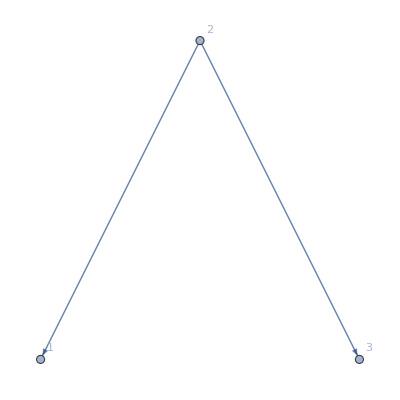
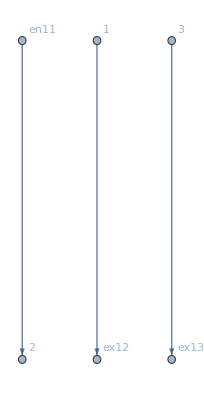
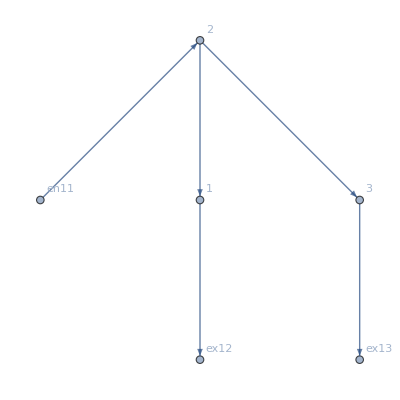
<|BG→-Graphics-,EntranceVertices→{2},InwardVertices→<|2→en11|>,InEdges→{en11->2},ExitVertices→{1,3},OutwardVertices→<|1→ex12,3→ex13|>,OutEdges→{1->ex12,3->ex13},AuxiliaryGraph→-Graphics-,FG→-Graphics-,VL→{1,2,3},EL→{1->ex12,2->1,2->3,3->ex13,en11->2},BEL→{2->1,2->3},jargs→{{ex12,1->ex12},{1,2->1},{3,2->3},{ex13,3->ex13},{2,en11->2},{1,1->ex12},{2,2->1},{2,2->3},{3,3->ex13},{en11,en11->2}},js→{j14,j15,j16,j17,j18,j19,j20,j21,j22,j23},jvars→<|{ex12,1->ex12}→j14,{1,2->1}→j15,{3,2->3}→j16,{ex13,3->ex13}→j17,{2,en11->2}→j18,{1,1->ex12}→j19,{2,2->1}→j20,{2,2->3}→j21,{3,3->ex13}→j22,{en11,en11->2}→j23|>,FVL→{1,2,3,en11,ex12,ex13},AllTransitions→{{1,1->ex12,2->1},{1,2->1,1->ex12},{2,2->1,2->3},{2,2->1,en11->2},{2,2->3,2->1},{2,2->3,en11->2},{2,en11->2,2->1},{2,en11->2,2->3},{3,2->3,3->ex13},{3,3->ex13,2->3}},jts→{jt24,jt25,jt26,jt27,jt28,jt29,jt30,jt31,jt32,jt33},jtvars→<|{1,1->ex12,2->1}→jt24,{1,2->1,1->ex12}→jt25,{2,2->1,2->3}→jt26,{2,2->1,en11->2}→jt27,{2,2->3,2->1}→jt28,{2,2->3,en11->2}→jt29,{2,en11->2,2->1}→jt30,{2,en11->2,2->3}→jt31,{3,2->3,3->ex13}→jt32,{3,3->ex13,2->3}→jt33|>,uargs→{{1,1->ex12},{2,2->1},{2,2->3},{3,3->ex13},{en11,en11->2},{ex12,1->ex12},{1,2->1},{3,2->3},{ex13,3->ex13},{2,en11->2}},us→{u34,u35,u36,u37,u38,u39,u40,u41,u42,u43},uvars→<|{1,1->ex12}→u34,{2,2->1}→u35,{2,2->3}→u36,{3,3->ex13}→u37,{en11,en11->2}→u38,{ex12,1->ex12}→u39,{1,2->1}→u40,{3,2->3}→u41,{ex13,3->ex13}→u42,{2,en11->2}→u43|>,EqPosCon→NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[j19]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[j22]&&NonNegative[j23]&&NonNegative[jt24]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[jt27]&&NonNegative[jt28]&&NonNegative[jt29]&&NonNegative[jt30]&&NonNegative[jt31]&&NonNegative[jt32]&&NonNegative[jt33],CurrentCompCon→MFGraphs`Private`CurrentCompCon$4840,EqCurrentCompCon→(j19==0||j14==0)&&(j20==0||j15==0)&&(j21==0||j16==0)&&(j22==0||j17==0)&&(j23==0||j18==0),TransitionCompCon→MFGraphs`Private`TransitionCompCon$4840,EqTransitionCompCon→(jt24==0||jt25==0)&&(jt26==0||jt28==0)&&(jt27==0||jt30==0)&&(jt29==0||jt31==0)&&(jt32==0||jt33==0),IncomingEdges→MFGraphs`Private`IncomingEdges$4840,OutgoingEdges→MFGraphs`Private`OutgoingEdges$4840,NoDeadEnds→{{1,1->ex12},{1,2->1},{2,2->1},{2,2->3},{2,en11->2},{3,2->3},{3,3->ex13}},NoDeadStarts→{{ex12,1->ex12},{2,2->1},{1,2->1},{3,2->3},{en11,en11->2},{2,2->3},{ex13,3->ex13}},CurrentSplitting→MFGraphs`Private`CurrentSplitting$4840,CurrentGathering→MFGraphs`Private`CurrentGathering$4840,EqBalanceSplittingCurrents→j19==jt24&&j15==jt25&&j20==jt26+jt27&&j21==jt28+jt29&&j18==jt30+jt31&&j16==jt32&&j22==jt33,EqBalanceGatheringCurrents→j14==jt25&&j20==jt24&&j15==jt28+jt30&&j16==jt26+jt31&&j23==jt27+jt29&&j21==jt33&&j17==jt32,EntryArgs→{{2,en11->2}},EntryDataAssociation→<|{2,en11->2}→I1|>,EqEntryIn→j18==I1,NonZeroEntryCurrents→Positive[I1],ExitCosts→<|ex12→U1,ex13→U2|>,ExitValues→MFGraphs`Private`ExitValues$4840,EqExitValues→u39==U1&&u42==U2,SwitchingCosts→<|{1,1->ex12,2->1}→∞,{1,2->1,1->ex12}→0,{2,2->1,2->3}→S1,{2,2->1,en11->2}→∞,{2,2->3,2->1}→S2,{2,2->3,en11->2}→∞,{2,en11->2,2->1}→0,{2,en11->2,2->3}→0,{3,2->3,3->ex13}→0,{3,3->ex13,2->3}→∞,{1,1->ex12,1->ex12}→∞,{1,1->ex12,2->3}→∞,{1,1->ex12,3->ex13}→∞,{1,1->ex12,en11->2}→∞,{3,3->ex13,1->ex12}→∞,{3,3->ex13,2->1}→∞,{3,3->ex13,3->ex13}→∞,{3,3->ex13,en11->2}→∞,{2,en11->2,en11->2}→∞|>,OutRules→{{1,1->ex12,1->ex12}→∞,{1,1->ex12,2->1}→∞,{1,1->ex12,2->3}→∞,{1,1->ex12,3->ex13}→∞,{1,1->ex12,en11->2}→∞,{3,3->ex13,1->ex12}→∞,{3,3->ex13,2->1}→∞,{3,3->ex13,2->3}→∞,{3,3->ex13,3->ex13}→∞,{3,3->ex13,en11->2}→∞},InRules→{{2,2->1,en11->2}→∞,{2,2->3,en11->2}→∞,{2,en11->2,en11->2}→∞},Transu→MFGraphs`Private`Transu$4840,EqSwitchingConditions→u40≤u34&&u34≤∞&&u36≤S2+u35&&u43≤u35&&u35≤S1+u36&&u43≤u36&&u35≤∞&&u36≤∞&&u37≤∞&&u41≤u37,Compu→MFGraphs`Private`Compu$4840,EqCompCon→jt24==0&&(jt25==0||-u34+u40==0)&&(jt26==0||-S1+u35-u36==0)&&jt27==0&&(jt28==0||-S2-u35+u36==0)&&jt29==0&&(jt30==0||-u35+u43==0)&&(jt31==0||-u36+u43==0)&&(jt32==0||-u37+u41==0)&&jt33==0,EqValue→MFGraphs`Private`EqValue$4840,EqValueAuxiliaryEdges→-u38+u43==0&&-u34+u39==0&&-u37+u42==0,EqAllComp→(j19==0||j14==0)&&(j20==0||j15==0)&&(j21==0||j16==0)&&(j22==0||j17==0)&&(j23==0||j18==0)&&(jt24==0||jt25==0)&&(jt26==0||jt28==0)&&(jt27==0||jt30==0)&&(jt29==0||jt31==0)&&(jt32==0||jt33==0)&&jt24==0&&(jt25==0||-u34+u40==0)&&(jt26==0||-S1+u35-u36==0)&&jt27==0&&(jt28==0||-S2-u35+u36==0)&&jt29==0&&(jt30==0||-u35+u43==0)&&(jt31==0||-u36+u43==0)&&(jt32==0||-u37+u41==0)&&jt33==0,EqAll→NonNegative[j14]&&NonNegative[j15]&&NonNegative[j16]&&NonNegative[j17]&&NonNegative[j18]&&NonNegative[j19]&&NonNegative[j20]&&NonNegative[j21]&&NonNegative[j22]&&NonNegative[j23]&&NonNegative[jt24]&&NonNegative[jt25]&&NonNegative[jt26]&&NonNegative[jt27]&&NonNegative[jt28]&&NonNegative[jt29]&&NonNegative[jt30]&&NonNegative[jt31]&&NonNegative[jt32]&&NonNegative[jt33]&&j19==jt24&&j15==jt25&&j20==jt26+jt27&&j21==jt28+jt29&&j18==jt30+jt31&&j16==jt32&&j22==jt33&&j14==jt25&&j20==jt24&&j15==jt28+jt30&&j16==jt26+jt31&&j23==jt27+jt29&&j21==jt33&&j17==jt32&&j18==I1&&u39==U1&&u42==U2&&u40≤u34&&u34≤∞&&u36≤S2+u35&&u43≤u35&&u35≤S1+u36&&u43≤u36&&u35≤∞&&u36≤∞&&u37≤∞&&u41≤u37&&-u38+u43==0&&-u34+u39==0&&-u37+u42==0|>

```mathematica
DataToEquations[DataG[4]]
```

```mathematica
DataToGraph
```

```mathematica
Names["MFGraphs`*"]
```

{AtHead,AtTail,DataToEquations,DataToGraph,EE,OtherWay,RR,triple2path,UU}